```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
result=NDSolve[{u[t]==ueff Cos[2π f t]-R i[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==1000,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
```

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

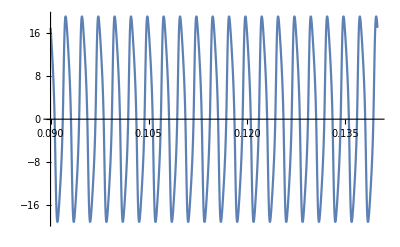

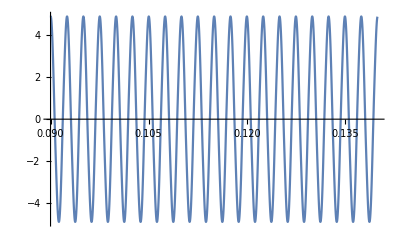

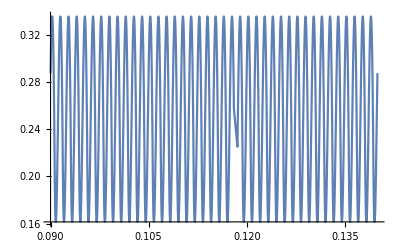

```mathematica
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14}]
Plot[i[t],{t,0.09,0.14}]
Plot[g[t],{t,0.09,0.14}]
```